```mathematica
<<Datasets`
```

Imported "Language`TryCatch`"

Imported "Language`Options`"

Imported "Language`Strings`"

```mathematica
ds=DatasetImport["D:\\Projects.github\\python_projects\\check_warehouse\\warehouses.csv"];
ds//Columns
```

{warehouse,x,y,items}

```mathematica
wp = Select[ds,(#items >= 0)&];
wn = Select[ds,(#items < 0)&];
```

```mathematica
cp=wp[[All, {"x","y"}]]//ToList;
cn=wn[[All, {"x","y"}]]//ToList;
```

```mathematica
<<Plots`
```

Imported "Coordinates`"

Imported "Language`"

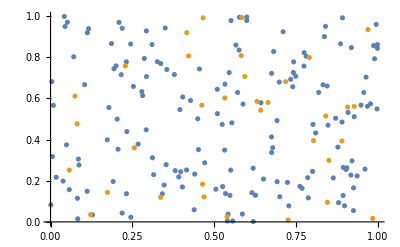

```mathematica
ListPointPlot[{cp, cn}]
```